```mathematica
(*R3*)
```

```mathematica
Quit
```

```mathematica
ds2 = dd[ρ]^2 + ρ^2*dd[ϕ]^2 + dd[z]^2
```

𝕕[z]^2+𝕕[ρ]^2+ρ^2 𝕕[ϕ]^2

```mathematica
$Assumptions= And[0<ϕ<2*π,ρ>0, ϕ∈Reals, z∈Reals];
metricsign=1;
SetDirectory["~/Downloads"];
<<diffgeo.m
```

ds2 = σ^2 (𝕕[σ]^2/(-P0^2 (1+P0^2)+σ^2+σ^4)+𝕕[τ]^2)

```mathematica
$Assumptions= And[ σ∈Reals, τ∈Reals];
hypersurface[{σ,τ},{ϕ->τ,ρ->Cosh[σ], z->σ}]
```

Warning: Only ambient coordinates must be assigned values in the parametrization!

$Aborted

```mathematica
ext = HSextrinsic
```

```mathematica
coord=HScoord
metric=HSmetric
```

```mathematica
<<diffgeo.m
```

```mathematica
(*compute K_{ab}K^{ab}*)
```

```mathematica
pot =  contract[ext**ext,{1,3}, {2,4}]
```

```mathematica
-scalarLaplacian[f[σ]]
```

```mathematica
(*find negative mode*)
```

```mathematica
DSolve[{f[0]==1, f'[0]==0,-scalarLaplacian[f[σ]]-pot* f[σ]==λ*f[σ]},f[σ],σ,Assumptions->{-1<λ<0} ]
```

```mathematica
NDSolve[{f[0]==1, f'[0]==0, f''[σ]+ (2*Sech[σ]^2+5*Cosh[σ]^2)*f[σ]==0},f,{σ,0,5}][[1]]
```

```mathematica
g[λ_] := f[5]/.(NDSolve[{f[0]==1, f'[0]==0, f''[σ]+ (2*Sech[σ]^2+λ*Cosh[σ]^2)*f[σ]==0},f,{σ,0,5}][[1]])
```

```mathematica
g[-1]
```

```mathematica
Plot[g[λ],{λ,-0.7,0}]
```

-Graphics-

```mathematica
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
(*H3 following ref 21*)
```

```mathematica
Quit
ClearAll["Global`*"];
```

```mathematica
ds2 = (1/(1+P^2))dd[P]^2 + (1+P^2)dd[z]^2 + P^2dd[ϕ]^2
```

dd[P]^2/(1+P^2)+(1+P^2) dd[z]^2+P^2 dd[ϕ]^2

```mathematica
SetDirectory["~/Downloads"];
```

```mathematica
<<diffgeo.m
```

coord = {P,z,ϕ}

```mathematica
inverse
```

{{1+P^2,0,0},{0,1/(1+P^2),0},{0,0,1/P^2}}

```mathematica
RicciTensor
```

{{-2/(1+P^2),0,0},{0,-2 (1+P^2),0},{0,0,-2 P^2}}

```mathematica
Clear[P0]
```

```mathematica
P0=2;
```

```mathematica
hypersurface[{σ,τ},{P->σ,z->h[σ],ϕ->τ}]
```

```mathematica
(*hypersurface[{σ,τ},{ϕ->τ,P->σ,z->(P0/(Sqrt[1+P0^2]*Sqrt[1+2*P0^2]))*((1+P0^2)EllipticF[ArcCos[P0/σ],Sqrt[(1+P0^2)/(1+2*P0^2)]] - P0^2*EllipticPi[ArcCos[P0/σ],1/(1+P0^2),Sqrt[(1+P0^2)/(1+2*P0^2)]])}]*)
```

```mathematica
HSextrinsicTrace;
```

```mathematica
(*h[σ_]:= (P0/(Sqrt[1+P0^2]*Sqrt[1+2*P0^2]))*((1+P0^2)EllipticF[ArcCos[P0/σ],Sqrt[(1+P0^2)/(1+2*P0^2)]] - P0^2*EllipticPi[ArcCos[P0/σ],1/(1+P0^2),Sqrt[(1+P0^2)/(1+2*P0^2)]])*)
```

```mathematica
f[σ_]:=-(P0*Sqrt[1+P0^2])/((1+σ^2)*Sqrt[σ^4+σ^2-P0^4-P0^2])
h'[σ_]:=f[σ]
h''[σ_]:=f'[σ]
```

```mathematica
HSextrinsicTrace;
```

```mathematica
Plot[HSextrinsicTrace,{σ,P0,80},PlotRange->All]
```

Plot::plln: Limiting value P0 in {σ,P0,80} is not a machine-sized real number.

Plot[HSextrinsicTrace,{σ,P0,80},PlotRange→All]

```mathematica
metric=FullSimplify[HSmetric]
coord=HScoord
```

{{σ^2/(-P0^2 (1+P0^2)+σ^2+σ^4),0},{0,σ^2}}

{σ,τ}

```mathematica
ext=HSextrinsic //Simplify
```

{{-(P0 √(1+P0^2) σ √Abs[P0^2+P0^4-σ^2 (1+σ^2)])/((-P0^2-P0^4+σ^2+σ^4)^(3/2) Abs[σ]),0},{0,(P0 √(1+P0^2) σ √Abs[P0^2+P0^4-σ^2 (1+σ^2)])/(√(-P0^2-P0^4+σ^2+σ^4) Abs[σ])}}

```mathematica
HSunitNormal
```

{(P0 √(1+P0^2))/((1+σ^2) √(-P0^2-P0^4+σ^2+σ^4) √Abs[1/(1+σ^2)+(P0^2 (1+P0^2))/((1+σ^2) (-P0^2-P0^4+σ^2+σ^4))]),1/(√Abs[1/(1+σ^2)+(P0^2 (1+P0^2))/((1+σ^2) (-P0^2-P0^4+σ^2+σ^4))]),0}

```mathematica
<<diffgeo.m
```

ds2 = σ^2 (𝕕[σ]^2/(-P0^2 (1+P0^2)+σ^2+σ^4)+𝕕[τ]^2)

```mathematica
inverse;
```

```mathematica
pot = contract[ext**ext,{1,3}, {2,4}]
```

(2 P0^2 (1+P0^2) Abs[P0^2+P0^4-σ^2 (1+σ^2)])/(σ^4 (-P0^2-P0^4+σ^2+σ^4))

```mathematica
pot = contract[ext.inverse.ext]
```

Piecewise[{{-40/σ^4, -2<σ<2}, {40/σ^4, True}}]

```mathematica
scalarLaplacian[a[σ,τ]]
```

(a^(0,2)[σ,τ]+(σ+2 σ^3) a^(1,0)[σ,τ]+(-P0^2-P0^4+σ^2+σ^4) a^(2,0)[σ,τ])/σ^2

```mathematica
Solve[scalarLaplacian[a[σ]] + (2 (P0^2+P0^4)/σ^4)*a[σ] ==-(λ-2) a[σ] /. { σ->P0},a'[P0]][[1]][[1]]
```

a'[P0]→(-2 a[P0]-P0^2 λ a[P0])/(P0 (1+2 P0^2))

```mathematica
scalarLaplacian[a[σ]] + (2 (P0^2+P0^4)/σ^4)*a[σ] ==-λ a[σ] /.{σ->z}
```

(2 (P0^2+P0^4) a[z])/z^4+((z+2 z^3) a'[z]+(-P0^2-P0^4+z^2+z^4) a''[z])/z^2==-λ a[z]

```mathematica
(* BC: normalized at P0 and field decays at infinity.
Impose with shooting method. Set derivative at P0 to 0 (why 0???) and find where it decays to 0 at infinity (we will evaluate at 5 and consider this infinity)  *)
```

```mathematica
ClearAll
```

ClearAll

```mathematica
guess[σ_] :=(c0+Sum[c[i]*σ^{i},{i,1,10}])
guess1[σ_] := D[guess[σ],σ]
guess2[σ_] := D[guess[σ],{σ,2}]
```

```mathematica
function[a0_,a1_,a2_,z_] := (2(P0^2+P0^4)a0+(P0+z)^2(P0+z+2 (P0+z)^3)a1 +(P0+z)^2(-P0^2-P0^4+(P0+z)^2+(P0+z)^4) a2+(P0+z)^4(λ-2) a0)
```

```mathematica
Expand[(function[guess[σ],guess1[σ],guess2[σ],σ]-(2 c0 P0^2+2 c0 P0^4+c0 P0^4 λ+P0^3 c[1]+2 P0^5 c[1]))/σ] /.σ->0
```

{32 c0 λ+212 c[1]+16 λ c[1]+432 c[2]}

```mathematica
c1p = Solve[2 c0 P0^2+2 c0 P0^4+c0 P0^4 (λ-2)+P0^3 c[1]+2 P0^5 c[1]==0,c[1]][[1]][[1]]/.{c0->1}
c2p = Solve[4 c0 P0^3 λ+5 P0^2 c[1]+12 P0^4 c[1]+P0^4 (λ-2) c[1]+6 P0^3 c[2]+12 P0^5 c[2]==0/.c1p,c[2]][[1]][[1]]/.{c0->1}
```

c[1]→(-2-P0^2 λ)/(P0 (1+2 P0^2))

c[2]→(10+20 P0^2+3 P0^2 λ+2 P0^4 λ+P0^4 λ^2)/(6 P0^2 (1+2 P0^2)^2)

```mathematica
solution[σ_] := 1 + c[1](σ-P0) + c[2](σ-P0)^2 /.{c1p,c2p}
```

```mathematica
P0=0.1;
```

```mathematica
λ =0;
```

```mathematica
start = P0(1+0.001);
bc1 = solution[start];
bc2 = solution'[start];
b[λ_] := a[1500]/.(NDSolve[{a[start]==bc1, a'[start]==bc2, -scalarLaplacian[a[σ]] - (2 (P0^2+P0^4)/σ^4)*a[σ] ==λ a[σ]},a,{σ,start,1500}][[1]])
```

```mathematica
Plot[b[λ],{λ,-60,-50}]
```

-Graphics-

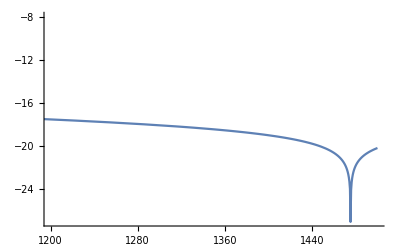

```mathematica
Plot[Log[Abs[a[s]]]/.(NDSolve[{a[start]==bc1, a'[start]==bc2, -scalarLaplacian[a[σ]] - (2 (P0^2+P0^4)/σ^4)*a[σ] ==λ a[σ] },a,{σ,start,2000}][[1]] ),{s,start,1500},PlotRange->{{1200,1500},Automatic}]
```

```mathematica
Clear[test]
Clear[P0]
Clear[λ]
Clear[start]
```

```mathematica
start = P0(1.00001);
bc1 = solution[start];
bc2 = solution'[start];
test[p_] := ParametricNDSolveValue[{a[start]==bc1, a'[start]==bc2, 2*(P0^2+P0^4)a[σ]+(σ)^2(σ+2 (σ)^3)a'[σ] +(σ)^2(-P0^2-P0^4+(σ)^2+(σ)^4) a''[σ]+(σ)^4(λ-2) a[σ]==0},a[15000],{σ,start,15000},{λ}]/.P0->p
```

```mathematica
λ/.FindRoot[test[0.513][λ],{λ,-10}][[1]]
```

-0.0271432

```mathematica
Table[λ/.FindRoot[test[p][λ],{λ,-10}][[1]],{p,0.35,0.6,0.05}]
```

{-2.70299,-1.6286,-0.893269,-0.368368,0.0190865,0.313012}

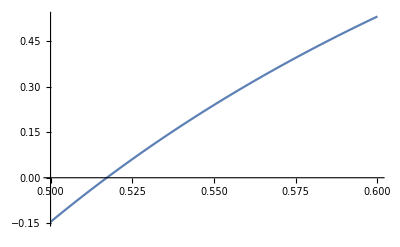

```mathematica
Plot[{λ/.FindRoot[test[p][λ],{λ,-10}][[1]]},{p,0.5,0.6}]
```

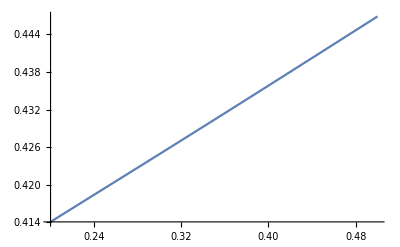

```mathematica
Plot[{λ/.FindRoot[test[p][λ],{λ,0.1}][[1]]},{p,0.2,0.5}]
```

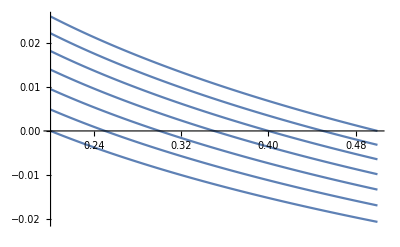

```mathematica
Plot[Table[test[p][λ]/. λ->Out[275][[i]],{i,1,7}],{p,0.2,0.5}]
```

```mathematica
test[0.2][λ]
```

ParametricFunction[<>][λ]

```mathematica
Table[test[0.2][λ]/. λ->Out[275][[i]],{i,1,7}]
```

{-1.17957×10^-7,0.00486153,0.00949173,0.0139177,0.0181473,0.0221787,0.026006}

```mathematica
Table[Exp[{λ/.FindRoot[test[p][λ],{λ,-1}][[1]]}],{p,0.55,0.6,0.01}]
```

{{1.57208},{2.85329},{1034.99},{0.268127},{0.280348},{0.29249}}

```mathematica
Table[{λ/.FindRoot[test[0.2][λ],{λ,-15}][[1]]},{p,0.2,0.6,0.01}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401},{-10.0401}}

```mathematica
largeS[σ_]:=DSolve[2 σ a'[σ] + σ^2 a''[σ]+ t a[σ]/σ^4  ==-λ a[σ]/.λ->-3.,a,σ] [[1]]
```

```mathematica
DSolve[ a'[σ] + σ a''[σ]==-λ σ a[σ],a,σ]
```

{{a→Function[{σ},BesselJ[0,√λ σ] C[1]+BesselY[0,√λ σ] C[2]]}}

```mathematica
BesselJ[0,ⅈ x]
```

BesselJ[0,ⅈ x]

```mathematica
Plot[BesselY[0,ⅈ x],{x,0.1,2}]
```

-Graphics-

```mathematica
N[BesselY[0,ⅈ 2]]
```

-0.0725071+2.27959 ⅈ

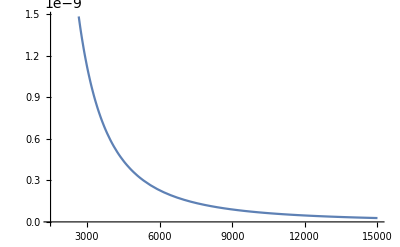

```mathematica
Plot[0.6011326402561157 (1/σ)^0.5000000000000002 BesselJ[0.9013878188659973,0.30463092423455634/σ^2],{σ,1500,15000}]
```

```mathematica
Simplify[a[σ] /.largeS[σ] /. t->2*(0.4^2+0.4^4) /. {C[1]->0,C[2]->1}]
```

0.601133 (1/σ)^0.5 BesselJ[0.901388,0.304631/σ^2]

```mathematica
FindRoot[BesselJ[1/4 √(1-4 λ),0.07106335201775948/1500^2]==0,{λ,0}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{λ→-117.309}

```mathematica
N[Gamma[1-1/4 √(1-4(-35.749999999999986))]]
```

1.1259×10^15

```mathematica
N[1-1/4 √(1-4(-35.75))]
```

-2.

```mathematica
(2 (P0^2+P0^4) a[σ])/σ^4+((σ+2 σ^3) a'[σ]+(-P0^2-P0^4+σ^2+σ^4) a''[σ])/σ^2==-λ a[σ] /.{a-> Function[σ,v[σ]/Sqrt[σ]]}//Simplify
```

((5 P0^2+5 P0^4+σ^2+(-1+4 λ) σ^4) v[σ]+4 σ ((P0^2+P0^4+σ^4) v'[σ]+σ (-P0^2-P0^4+σ^2+σ^4) v''[σ]))/(√σ)==0

```mathematica
DSolve[4(σ) a'[σ] + 4(σ^2+1-t/σ^2) a''[σ] +(-1+4λ) a[σ]+(1/σ^2 )a[σ]  ==0 /.λ->-10.232,a,σ] [[1]]
```

$Aborted

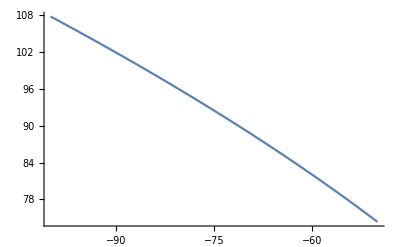

```mathematica
Plot[Log[Abs[Re[Hypergeometric2F1[1/4-1/4 √(1-4 λ),1/4+1/4 √(1-4 λ),1,-σ^2]]]]/.σ->50000,{λ,-50,-100}]
```

```mathematica
N[Hypergeometric2F1[1/4-1/4 √(1-4 λ),1/4+1/4 √(1-4 λ),1,-σ^2] /.λ->1.142 /.σ->10000]
```

-0.0044654-8.27138×10^-12 ⅈ

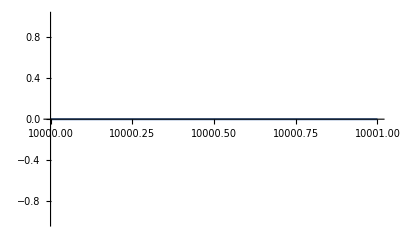

```mathematica
Plot[MeijerG[{{},{1-1/4 √(1-4 λ),1/4 (4+√(1-4 λ))}},{{1/4,1/4},{}},-σ^2]/.λ->-1.2342, {σ,10000,10001}]
```

```mathematica
N[MeijerG[{{},{1-1/4 √(1-4 λ),1/4 (4+√(1-4 λ))}},{{1/4,1/4},{}},-σ^2]/.λ->-10 /. σ->10]
```

0.

```mathematica
Series[MeijerG[{{},{1-1/4 √(1-4 λ),1/4 (4+√(1-4 λ))}},{{1/4,1/4},{}},-σ^2] ,{σ,∞,1}]
```

O[1/σ]^2

```mathematica
N[MeijerG[{{},{1-1/4 √(1-4 λ),1/4 (4+√(1-4 λ))}},{{1/4,1/4},{}},50] ]
```

0.

```mathematica
Plot[HeunG[(-1+√(1+4 t))/(-1-√(1+4 t)),1/(8 (1+√(1+4 t))),1/2 (-1/2+(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))+(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t)))-√((1/2-(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))-(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t))))^2+1/4 (1-4 λ))),1/2 (-1/2+(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))+(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t)))+√((1/2-(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))-(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t))))^2+1/4 (1-4 λ))),1/2,(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t))),(2 σ^2)/(-1-√(1+4 t))] /.t->1/100000 /. λ->-10.232,{σ,100,1000}]
```

-Graphics-

```mathematica
N[HeunG[(-1+√(1+4 t))/(-1-√(1+4 t)),1/(8 (1+√(1+4 t))),1/2 (-1/2+(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))+(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t)))-√((1/2-(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))-(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t))))^2+1/4 (1-4 λ))),1/2 (-1/2+(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))+(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t)))+√((1/2-(1+2 t-√(1+4 t))/(2 √(1+4 t) (-1+√(1+4 t)))-(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t))))^2+1/4 (1-4 λ))),1/2,(1+2 t+√(1+4 t))/(2 √(1+4 t) (1+√(1+4 t))),(2 σ^2)/(-1-√(1+4 t))] /.t->1/100 /. λ->-10/.σ->1.1,2]
```

Divide::indet: Indeterminate expression 0/0 encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

Divide::infy: Infinite expression (4.5×10^-6)/0 encountered.

Power::infy: Infinite expression 1/0 encountered.

$Aborted

```mathematica
N[HeunG[-1.1,0.06,-1.6,1.6,0.5,0.5,-100]]
```

HeunG[-1.1,0.06,-1.6,1.6,0.5,0.5,-100.]

```mathematica
pm =0.5163344740613613;
```

```mathematica
zeta[p0_,σ_] := p0/(Sqrt[1+p0^2]Sqrt[1+2p0^2])(
(1+p0^2)EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2p0^2)]
-p0^2EllipticPi[1/(1+p0^2),ArcCos[p0/σ],(1+p0^2)/(1+2p0^2)]
)
dzeta = D[zeta[p0,σ],p0] //FullSimplify
```

(-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) √(1-p0^2/σ^2) σ^3 √((p0^2 (1+p0^2+σ^2))/((1+2 p0^2) σ^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/(√(1+p0^2) (1+2 p0^2)^(3/2) √(1-p0^2/σ^2) σ^3 √((p0^2 (1+p0^2+σ^2))/((1+2 p0^2) σ^2)))

```mathematica
zeta[P0,σ]
```

(P0 ((1+P0^2) EllipticF[ArcCos[P0/σ],(1+P0^2)/(1+2 P0^2)]-P0^2 EllipticPi[1/(1+P0^2),ArcCos[P0/σ],(1+P0^2)/(1+2 P0^2)]))/(√(1+P0^2) √(1+2 P0^2))

```mathematica
nor[p0_,σ_] := Sqrt[D[zeta[p0,σ],σ]^2(1+σ^2)+1/(1+σ^2)]
nnorm = -1/nor[p0,σ] //Simplify
```

-1/(√(σ^2/(-p0^2-p0^4+σ^2+σ^4)))

```mathematica
Clear[zeroMode]
```

```mathematica
zeroMode[σ_] := nnorm * dzeta
```

```mathematica
zeroMode[σ]
```

-(-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/((1+2 p0^2)^(3/2) σ √((1+p0^2) (-p0^2+σ^2)) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) √(σ^2/(-p0^2-p0^4+σ^2+σ^4)))

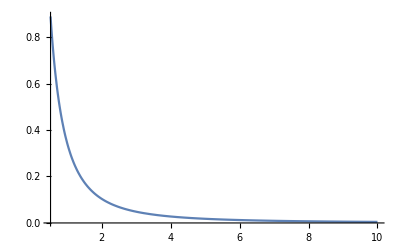

```mathematica
Plot[zeroMode[σ] /.p0->pm,{σ,pm,10},PlotRange->All]
```

```mathematica
FindRoot[(zeroMode[σ]/.p0->pm)==0,{σ,10^5}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{σ→7.52935×10^14}

```mathematica
FindRoot[2 EllipticE[(1+p0^2)/(1+2 p0^2)]-EllipticK[(1+p0^2)/(1+2 p0^2)],{p0,1} ]
```

{p0→0.516334}

```mathematica
EllipticK[(1+p0^2)/(1+2 p0^2)] /.p0->pm
```

2.32105

```mathematica
Series[(zeroMode[σ]),{σ,∞,5}]
```

(2 EllipticE[(1+p0^2)/(1+2 p0^2)]-EllipticK[(1+p0^2)/(1+2 p0^2)])/(√(1+p0^2) √(1+2 p0^2) σ)+(-2 EllipticE[(1+p0^2)/(1+2 p0^2)]+EllipticK[(1+p0^2)/(1+2 p0^2)])/(2 √(1+p0^2) √(1+2 p0^2) σ^3)+(p0+4 p0^3+4 p0^5)/(3 √(1+p0^2) √(p0^2/(1+2 p0^2)) (1+2 p0^2)^(3/2) σ^4)+(3 (2 EllipticE[(1+p0^2)/(1+2 p0^2)]-EllipticK[(1+p0^2)/(1+2 p0^2)]))/(8 √(1+p0^2) √(1+2 p0^2) σ^5)+O[1/σ]^6

```mathematica
FullSimplify[zeroMode[σ],Assumptions->σ>pm>0 ]
```

-(-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/(σ^2 ((1+2 p0^2)/(1+σ^2))^(3/2) √((1+p0^2) (-p0^2+σ^2)) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) √((-(1+σ^2)^5+p0^2 (4+6 σ^2+4 σ^4+σ^6)+p0^4 (4+6 σ^2+4 σ^4+σ^6))/(p0^2+p0^4-σ^2 (1+σ^2))))

```mathematica
zzeroMode[σ_] := -(-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/(σ^2 ((1+2 p0^2)/(1+σ^2))^(3/2) √(1+p0^2) √(1/(1+2 p0^2)) √((1+σ^2)^5-p0^2 (4+6 σ^2+4 σ^4+σ^6)-p0^4 (4+6 σ^2+4 σ^4+σ^6)))
```

```mathematica
zzeroMode[σ]
```

-(-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/(√(1+p0^2) √(1/(1+2 p0^2)) σ^2 ((1+2 p0^2)/(1+σ^2))^(3/2) √((1+σ^2)^5-p0^2 (4+6 σ^2+4 σ^4+σ^6)-p0^4 (4+6 σ^2+4 σ^4+σ^6)))

```mathematica
zzeroMode[σ] /.p0->pm
```

-(0.579536 (-0.348709+0.516334 σ^2-0.639339 σ √(-0.266601+σ^2) √(1.2666+σ^2) (2 EllipticE[ArcCos[0.516334/σ],0.826115]-EllipticF[ArcCos[0.516334/σ],0.826115])))/(σ^2 (1/(1+σ^2))^(3/2) √((1+σ^2)^5-0.337678 (4+6 σ^2+4 σ^4+σ^6)))

```mathematica
Series[zzeroMode[σ],{σ,p0,2},Assumptions->{σ>p0>0}]
```

(p0 ((1+p0^2)/(1+2 p0^2))^(3/2) (1+2 p0^2)^(3/2))/(1+p0^2)-1/(√p0 (1+p0^2)^2 √(-p0+σ))((1+p0^2)/(1+2 p0^2))^(3/2) √(1+2 p0^2) (-2 √(-p0 (p0-σ))-6 p0^2 √(-p0 (p0-σ))-4 p0^4 √(-p0 (p0-σ))+4 √p0 √(-p0+σ)+10 p0^(5/2) √(-p0+σ)+22 p0^(9/2) √(-p0+σ)+44 p0^(13/2) √(-p0+σ)+41 p0^(17/2) √(-p0+σ)+20 p0^(21/2) √(-p0+σ)+4 p0^(25/2) √(-p0+σ)) (σ-p0)+1/(6 p0^(3/2) (1+p0^2)^3 √(-p0+σ))((1+p0^2)/(1+2 p0^2))^(3/2) √(1+2 p0^2) (-26 √(-p0 (p0-σ))-104 p0^2 √(-p0 (p0-σ))-322 p0^4 √(-p0 (p0-σ))-772 p0^6 √(-p0 (p0-σ))-1020 p0^8 √(-p0 (p0-σ))-732 p0^10 √(-p0 (p0-σ))-288 p0^12 √(-p0 (p0-σ))-48 p0^14 √(-p0 (p0-σ))+36 √p0 √(-p0+σ)+150 p0^(5/2) √(-p0+σ)+504 p0^(9/2) √(-p0+σ)+1578 p0^(13/2) √(-p0+σ)+4545 p0^(17/2) √(-p0+σ)+9657 p0^(21/2) √(-p0+σ)+13512 p0^(25/2) √(-p0+σ)+12396 p0^(29/2) √(-p0+σ)+7497 p0^(33/2) √(-p0+σ)+2934 p0^(37/2) √(-p0+σ)+684 p0^(41/2) √(-p0+σ)+72 p0^(45/2) √(-p0+σ)) (σ-p0)^2+O[σ-p0]^3

```mathematica
FullSimplify[Out[113],Assumptions->{σ>p0>0}]
```

p0 √(1+p0^2)-((2 √(1+p0^2)+4 √(p0^4+p0^6)+p0^4 √(1+p0^2) (18+44 p0^2+41 p0^4+20 p0^6+4 p0^8)) (σ-p0))/(1+3 p0^2+2 p0^4)+1/(6 p0^(3/2) (1+p0^2)^2 (1+2 p0^2))(10 √(p0+p0^3)+46 √(p0^5+p0^7)+182 √(p0^9+p0^11)+806 √(p0^13+p0^15)+3525 √(p0^17+p0^19)+8925 √(p0^21+p0^23)+13224 √(p0^25+p0^27)+12348 √(p0^29+p0^31)+7497 √(p0^33+p0^35)+2934 √(p0^37+p0^39)+684 √(p0^41+p0^43)+72 √(p0^45+p0^47)) (σ-p0)^2+O[σ-p0]^3

```mathematica
Series[D[zzeroMode[σ],σ],{σ,p0,2},Assumptions->{σ>p0>0}]
```

1/((1+p0^2) (1+2 p0^2)^(3/2))(-2 √((1+p0^2)/(1+2 p0^2))-7 p0^2 √((1+p0^2)/(1+2 p0^2))-4 p0^4 √((1+p0^2)/(1+2 p0^2))+4 p0^6 √((1+p0^2)/(1+2 p0^2))-5 p0^2 √((1+2 p0^2)/(1+p0^2))-29 p0^4 √((1+2 p0^2)/(1+p0^2))-68 p0^6 √((1+2 p0^2)/(1+p0^2))-85 p0^8 √((1+2 p0^2)/(1+p0^2))-61 p0^10 √((1+2 p0^2)/(1+p0^2))-24 p0^12 √((1+2 p0^2)/(1+p0^2))-4 p0^14 √((1+2 p0^2)/(1+p0^2))-p0 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √(-p0/(p0-σ)) √((-1-2 p0^2)/(p0 (p0-σ)))-3 p0^3 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √(-p0/(p0-σ)) √((-1-2 p0^2)/(p0 (p0-σ)))-2 p0^5 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √(-p0/(p0-σ)) √((-1-2 p0^2)/(p0 (p0-σ)))-√((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(-p0 (p0-σ))-p0^2 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(-p0 (p0-σ))+√((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √(-p0/(p0-σ)) √((-1-2 p0^2)/(p0 (p0-σ))) σ+3 p0^2 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √(-p0/(p0-σ)) √((-1-2 p0^2)/(p0 (p0-σ))) σ+2 p0^4 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √(-p0/(p0-σ)) √((-1-2 p0^2)/(p0 (p0-σ))) σ+2 p0^(5/2) √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(-p0+σ)+2 p0^(9/2) √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(-p0+σ))+1/(3 p0^(3/2) (1+p0^2)^2 (1+2 p0^2)^(3/2) √(-p0+σ))(-12 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))-54 p0^2 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))-66 p0^4 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+24 p0^8 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))-30 p0^2 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-204 p0^4 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-582 p0^6 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-918 p0^8 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-876 p0^10 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-510 p0^12 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-168 p0^14 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-24 p0^16 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+30 √p0 √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+141 p0^(5/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+303 p0^(9/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+474 p0^(13/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+498 p0^(17/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+225 p0^(21/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-42 p0^(25/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-84 p0^(29/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-24 p0^(33/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-8 p0 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)-20 p0^3 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)-40 p0^5 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)-196 p0^7 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)-360 p0^9 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)-300 p0^11 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)-132 p0^13 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)-24 p0^15 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((1+2 p0^2)/p0) √(-p0+σ)+45 p0^(5/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+306 p0^(9/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+1467 p0^(13/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+5487 p0^(17/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+13875 p0^(21/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+23130 p0^(25/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+25944 p0^(29/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+19905 p0^(33/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+10431 p0^(37/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+3618 p0^(41/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+756 p0^(45/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)+72 p0^(49/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)) (σ-p0)+1/(30 p0^(5/2) (1+p0^2)^3 (1+2 p0^2)^(3/2) √(-p0+σ))(380 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+2450 p0^2 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+7520 p0^4 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+15050 p0^6 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+19760 p0^8 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+14660 p0^10 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+3660 p0^12 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))-2520 p0^14 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))-2160 p0^16 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))-480 p0^18 √((1+p0^2)/(1+2 p0^2)) √(-p0 (p0-σ))+350 p0^2 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+3330 p0^4 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+24530 p0^6 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+120340 p0^8 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+366830 p0^10 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+725610 p0^12 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+974930 p0^14 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+915260 p0^16 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+606520 p0^18 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+280980 p0^20 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+87480 p0^22 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+16560 p0^24 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))+1440 p0^26 √((1+2 p0^2)/(1+p0^2)) √(-p0 (p0-σ))-660 √p0 √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-4380 p0^(5/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-14520 p0^(9/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-37890 p0^(13/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-90720 p0^(17/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-179415 p0^(21/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-254715 p0^(25/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-236730 p0^(29/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-126150 p0^(33/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-17595 p0^(37/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+24120 p0^(41/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+18360 p0^(45/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+5760 p0^(49/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)+720 p0^(53/2) √((1+p0^2)/(1+2 p0^2)) √(-p0+σ)-300 p0^(5/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-3540 p0^(9/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-29070 p0^(13/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-175920 p0^(17/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-849075 p0^(21/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-3113190 p0^(25/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-8271705 p0^(29/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-15881025 p0^(33/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-22384845 p0^(37/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-23555070 p0^(41/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-18705330 p0^(45/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-11233485 p0^(49/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-5055705 p0^(53/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-1663200 p0^(57/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-379800 p0^(61/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-54000 p0^(65/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-3600 p0^(69/2) √((1+2 p0^2)/(1+p0^2)) √(-p0+σ)-136 ⅈ p0 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-648 ⅈ p0^3 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-2048 ⅈ p0^5 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-4176 ⅈ p0^7 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-15560 ⅈ p0^9 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-59860 ⅈ p0^11 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-133280 ⅈ p0^13 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-178940 ⅈ p0^15 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-154520 ⅈ p0^17 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-88020 ⅈ p0^19 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-32580 ⅈ p0^21 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-7200 ⅈ p0^23 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)-720 ⅈ p0^25 √((1+p0^2)/(1+2 p0^2)) √(1+2 p0^2) √((-1-2 p0^2)/(p0 (p0-σ))) √(p0-σ) √(-p0+σ)) (σ-p0)^2+O[σ-p0]^(5/2)

```mathematica
FullSimplify[Out[102],Assumptions->{σ>p0>0}]
```

(-2-p0^2 (4+18 p0^2+44 p0^4+41 p0^6+20 p0^8+4 p0^10))/(√(1+p0^2) (1+2 p0^2))+((10+46 p0^2+182 p0^4+p0^6 (806+3525 p0^2+8925 p0^4+13224 p0^6+9 p0^8 (1372+833 p0^2+326 p0^4+76 p0^6+8 p0^8))) (σ-p0))/(3 (1+p0^2)^(3/2) (p0+2 p0^3))+1/(10 p0^2 (1+p0^2)^(5/2) (1+2 p0^2))(-48-p0^2 (224+824 p0^2+4808 p0^4+5 p0^6 (5204+p0^2 (30080+127612 p0^2+347920 p0^4+632281 p0^6+3 p0^8 (267923+246244 p0^2+166368 p0^4+82653 p0^6+40 p0^8 (741+183 p0^2+28 p0^4+2 p0^6)))))) (σ-p0)^2+O[σ-p0]^4

```mathematica
FullSimplify[(1/(3 p0^(3/2) (1+p0^2)^2 (1+2 p0^2))(10 √(p0+p0^3)+46 √(p0^5+p0^7)+182 √(p0^9+p0^11)+806 √(p0^13+p0^15)+3525 √(p0^17+p0^19)+8925 √(p0^21+p0^23)+13224 √(p0^25+p0^27)+12348 √(p0^29+p0^31)+7497 √(p0^33+p0^35)+2934 √(p0^37+p0^39)+684 √(p0^41+p0^43)+72 √(p0^45+p0^47)) ),Assumptions->{p0>0}]
```

1/(3 p0^(3/2) (1+p0^2)^2 (1+2 p0^2))(10 √(p0+p0^3)+46 √(p0^5+p0^7)+182 √(p0^9+p0^11)+806 √(p0^13+p0^15)+3525 √(p0^17+p0^19)+8925 √(p0^21+p0^23)+13224 √(p0^25+p0^27)+12348 √(p0^29+p0^31)+7497 √(p0^33+p0^35)+2934 √(p0^37+p0^39)+684 √(p0^41+p0^43)+72 √(p0^45+p0^47))

```mathematica
Series[(10+46 p0^2+182 p0^4+p0^6 (806+3525 p0^2+8925 p0^4+13224 p0^6+9 p0^8 (1372+833 p0^2+326 p0^4+76 p0^6+8 p0^8)))/(3 (1+p0^2)^(3/2) (p0+2 p0^3)), {p0,0,10}]
```

10/(3 p0)+(11 p0)/3+(439 p0^3)/12+(3023 p0^5)/24+(116831 p0^7)/192+(151781 p0^9)/384+O[p0]^11

```mathematica
FullSimplify[Series[Out[156], {p0,0,10}],Assumptions->{σ>p0>0}]
```

10/(3 p0)+(11 p0)/3+(439 p0^3)/12+(3023 p0^5)/24+(116831 p0^7)/192+(151781 p0^9)/384+O[p0]^11

```mathematica
Series[zzeroMode[σ],{σ,p0,5}]
```

(-(√(1+p0^2) √(1/(1+2 p0^2)))/(p0^2 √(1+2 p0^2))+(√(1/(1+2 p0^2)) (2+4 p0^2+14 p0^4+16 p0^6+9 p0^8+2 p0^10) (σ-p0))/(p0^3 √(1+p0^2) √(1+2 p0^2))-((√(1/(1+2 p0^2)) (6+18 p0^2+62 p0^4+282 p0^6+851 p0^8+1473 p0^10+1550 p0^12+1032 p0^14+435 p0^16+108 p0^18+12 p0^20)) (σ-p0)^2)/(2 (p0^4 (1+p0^2)^(3/2) √(1+2 p0^2)))+(√(1/(1+2 p0^2)) (8+32 p0^2+104 p0^4+408 p0^6+2124 p0^8+10040 p0^10+31548 p0^12+64888 p0^14+91299 p0^16+91193 p0^18+66030 p0^20+34788 p0^22+13125 p0^24+3390 p0^26+540 p0^28+40 p0^30) (σ-p0)^3)/(2 p0^5 (1+p0^2)^(5/2) √(1+2 p0^2))-1/(8 (p0^6 (1+p0^2)^(7/2) √(1+2 p0^2)))(√(1/(1+2 p0^2)) (40+200 p0^2+680 p0^4+2512 p0^6+9932 p0^8+50460 p0^10+314148 p0^12+1516484 p0^14+4988943 p0^16+11480006 p0^18+19261139 p0^20+24338832 p0^22+23673110 p0^24+17946870 p0^26+10648660 p0^28+4922840 p0^30+1746835 p0^32+461720 p0^34+85960 p0^36+10080 p0^38+560 p0^40)) (σ-p0)^4+1/(8 p0^7 (1+p0^2)^(9/2) √(1+2 p0^2))√(1/(1+2 p0^2)) (48+288 p0^2+1056 p0^4+3840 p0^6+15360 p0^8+59728 p0^10+245816 p0^12+1677968 p0^14+11884482 p0^16+59067820 p0^18+203434780 p0^20+509538236 p0^22+967483057 p0^24+1435011080 p0^26+1697790855 p0^28+1624823258 p0^30+1268537220 p0^32+810900550 p0^34+423993570 p0^36+180224800 p0^38+61507047 p0^40+16499350 p0^42+3359160 p0^44+488880 p0^46+45360 p0^48+2016 p0^50) (σ-p0)^5+O[σ-p0]^6) (((-p0^3-2 p0^5)+2 p0^2 (σ-p0)+p0 (σ-p0)^2+O[σ-p0]^6)+(-1)^Floor[(π-Arg[-p0+σ]-Arg[(5 p0^4-10 p0^3 σ+10 p0^2 σ^2-5 p0 σ^3+σ^4)/p0^5])/(2 π)] (1/p0)^(1/2+1/2 Floor[Arg[(4 p0^4-10 p0^3 σ+10 p0^2 σ^2-5 p0 σ^3+σ^4)/p0^5]/(2 π)]) p0^(-3+1/2 Floor[Arg[(4 p0^4-10 p0^3 σ+10 p0^2 σ^2-5 p0 σ^3+σ^4)/p0^5]/(2 π)]) (-(2 (p0^4 √(p0^2) (1+2 p0^2) √(-p0 (p0-σ))) (σ-p0))/(√(-p0+σ))-(((-p0^3 √(p0^2)+10 p0^5 √(p0^2)) √(-p0 (p0-σ))) (σ-p0)^2)/(3 √(-p0+σ))-(((110 p0^4 √(p0^2)-(p0^2)^(3/2)) √(-p0 (p0-σ))) (σ-p0)^3)/(60 √(-p0+σ))+((625 p0^3+1844 p0^5+1060 p0^7) √(-p0 (p0-σ)) (σ-p0)^4)/(840 √(p0^2) (1+2 p0^2) √(-p0+σ))-(((45479 p0^2+246008 p0^4+601224 p0^6+687520 p0^8+286144 p0^10) √(-p0 (p0-σ))) (σ-p0)^5)/(60480 (√(p0^2) (1+2 p0^2)^3 √(-p0+σ)))+O[σ-p0]^6))

```mathematica
Series[D[D[zzeroMode[σ],σ],σ],{σ,p0,2},Assumptions->{σ>p0>0}]
```

1/(6 (1+p0^2)^(5/2) (1+2 p0^2)^(3/2) (σ-p0))p0^(5/2) √((1+p0^2)/(p0^2 (1+2 p0^2))) (32 √p0 √(1+p0^2)+224 p0^(5/2) √(1+p0^2)+763 p0^(9/2) √(1+p0^2)+1600 p0^(13/2) √(1+p0^2)+2040 p0^(17/2) √(1+p0^2)+1464 p0^(21/2) √(1+p0^2)+576 p0^(25/2) √(1+p0^2)+96 p0^(29/2) √(1+p0^2)-32 √(p0 (1+p0^2))-224 p0^2 √(p0 (1+p0^2))-763 p0^4 √(p0 (1+p0^2))-1600 p0^6 √(p0 (1+p0^2))-2040 p0^8 √(p0 (1+p0^2))-1464 p0^10 √(p0 (1+p0^2))-576 p0^12 √(p0 (1+p0^2))-96 p0^14 √(p0 (1+p0^2)))+1/(6 (1+p0^2)^(5/2) (1+2 p0^2)^(3/2))√((1+p0^2)/(p0^2 (1+2 p0^2))) (20 √(1+p0^2)+191 p0^2 √(1+p0^2)+826 p0^4 √(1+p0^2)+3103 p0^6 √(1+p0^2)+11874 p0^8 √(1+p0^2)+33990 p0^10 √(1+p0^2)+63612 p0^12 √(1+p0^2)+78168 p0^14 √(1+p0^2)+64482 p0^16 √(1+p0^2)+35856 p0^18 √(1+p0^2)+13104 p0^20 √(1+p0^2)+2880 p0^22 √(1+p0^2)+288 p0^24 √(1+p0^2)-59 p0^(3/2) √(p0 (1+p0^2))-278 p0^(7/2) √(p0 (1+p0^2))-763 p0^(11/2) √(p0 (1+p0^2))-1600 p0^(15/2) √(p0 (1+p0^2))-2040 p0^(19/2) √(p0 (1+p0^2))-1464 p0^(23/2) √(p0 (1+p0^2))-576 p0^(27/2) √(p0 (1+p0^2))-96 p0^(31/2) √(p0 (1+p0^2)))+1/(240 p0^2 (1+p0^2)^2 √(-p0 (1+2 p0^2) (p0-σ)))((1+p0^2)/(1+2 p0^2))^(3/2) √(-p0+σ) (1620 p0 √(-p0/(p0-σ))+9780 p0^3 √(-p0/(p0-σ))+18000 p0^5 √(-p0/(p0-σ))+25680 p0^7 √(-p0/(p0-σ))+47880 p0^9 √(-p0/(p0-σ))+46800 p0^11 √(-p0/(p0-σ))+23520 p0^13 √(-p0/(p0-σ))+4800 p0^15 √(-p0/(p0-σ))+2516 √(-p0 (p0-σ))+3803 p0^2 √(-p0 (p0-σ))+2987 p0^4 √(-p0 (p0-σ))+4400 p0^6 √(-p0 (p0-σ))+14850 p0^8 √(-p0 (p0-σ))+15840 p0^10 √(-p0 (p0-σ))+8360 p0^12 √(-p0 (p0-σ))+1760 p0^14 √(-p0 (p0-σ))-1620 √(-p0/(p0-σ)) σ-9780 p0^2 √(-p0/(p0-σ)) σ-18000 p0^4 √(-p0/(p0-σ)) σ-25680 p0^6 √(-p0/(p0-σ)) σ-47880 p0^8 √(-p0/(p0-σ)) σ-46800 p0^10 √(-p0/(p0-σ)) σ-23520 p0^12 √(-p0/(p0-σ)) σ-4800 p0^14 √(-p0/(p0-σ)) σ+8665 p0^(5/2) √(-p0+σ)+21285 p0^(9/2) √(-p0+σ)+18080 p0^(13/2) √(-p0+σ)-11130 p0^(17/2) √(-p0+σ)-21840 p0^(21/2) √(-p0+σ)-14280 p0^(25/2) √(-p0+σ)-3360 p0^(29/2) √(-p0+σ)) √(σ-p0)+1/(3 p0^(5/2) (1+p0^2)^(7/2) (1+2 p0^2)^(3/2) (p0-σ))√(-((1+p0^2) (p0-σ))/(1+2 p0^2)) (840 p0^(5/2) √(-((1+p0^2) (p0-σ)))+3288 p0^(9/2) √(-((1+p0^2) (p0-σ)))+11928 p0^(13/2) √(-((1+p0^2) (p0-σ)))+50202 p0^(17/2) √(-((1+p0^2) (p0-σ)))+213708 p0^(21/2) √(-((1+p0^2) (p0-σ)))+773982 p0^(25/2) √(-((1+p0^2) (p0-σ)))+2137320 p0^(29/2) √(-((1+p0^2) (p0-σ)))+4334901 p0^(33/2) √(-((1+p0^2) (p0-σ)))+6464619 p0^(37/2) √(-((1+p0^2) (p0-σ)))+7171218 p0^(41/2) √(-((1+p0^2) (p0-σ)))+5974632 p0^(45/2) √(-((1+p0^2) (p0-σ)))+3747717 p0^(49/2) √(-((1+p0^2) (p0-σ)))+1755378 p0^(53/2) √(-((1+p0^2) (p0-σ)))+599400 p0^(57/2) √(-((1+p0^2) (p0-σ)))+141840 p0^(61/2) √(-((1+p0^2) (p0-σ)))+20880 p0^(65/2) √(-((1+p0^2) (p0-σ)))+1440 p0^(69/2) √(-((1+p0^2) (p0-σ)))-32 p0 √(-((1+p0^2) (p0-σ))/p0)-224 p0^3 √(-((1+p0^2) (p0-σ))/p0)-704 p0^5 √(-((1+p0^2) (p0-σ))/p0)-1856 p0^7 √(-((1+p0^2) (p0-σ))/p0)-4448 p0^9 √(-((1+p0^2) (p0-σ))/p0)-7184 p0^11 √(-((1+p0^2) (p0-σ))/p0)-7008 p0^13 √(-((1+p0^2) (p0-σ))/p0)-4080 p0^15 √(-((1+p0^2) (p0-σ))/p0)-1344 p0^17 √(-((1+p0^2) (p0-σ))/p0)-192 p0^19 √(-((1+p0^2) (p0-σ))/p0)+72 √(-p0 (1+p0^2) (p0-σ))-288 p0^2 √(-p0 (1+p0^2) (p0-σ))-1200 p0^4 √(-p0 (1+p0^2) (p0-σ))-4560 p0^6 √(-p0 (1+p0^2) (p0-σ))-16974 p0^8 √(-p0 (1+p0^2) (p0-σ))-49392 p0^10 √(-p0 (1+p0^2) (p0-σ))-101106 p0^12 √(-p0 (1+p0^2) (p0-σ))-143820 p0^14 √(-p0 (1+p0^2) (p0-σ))-143322 p0^16 √(-p0 (1+p0^2) (p0-σ))-100434 p0^18 √(-p0 (1+p0^2) (p0-σ))-48960 p0^20 √(-p0 (1+p0^2) (p0-σ))-15984 p0^22 √(-p0 (1+p0^2) (p0-σ))-3168 p0^24 √(-p0 (1+p0^2) (p0-σ))-288 p0^26 √(-p0 (1+p0^2) (p0-σ))-80 p0^3 √((-p0+σ)/(p0 (1+p0^2)))-544 p0^5 √((-p0+σ)/(p0 (1+p0^2)))-1952 p0^7 √((-p0+σ)/(p0 (1+p0^2)))-9440 p0^9 √((-p0+σ)/(p0 (1+p0^2)))-45424 p0^11 √((-p0+σ)/(p0 (1+p0^2)))-142264 p0^13 √((-p0+σ)/(p0 (1+p0^2)))-286256 p0^15 √((-p0+σ)/(p0 (1+p0^2)))-387864 p0^17 √((-p0+σ)/(p0 (1+p0^2)))-365480 p0^19 √((-p0+σ)/(p0 (1+p0^2)))-242528 p0^21 √((-p0+σ)/(p0 (1+p0^2)))-112392 p0^23 √((-p0+σ)/(p0 (1+p0^2)))-34992 p0^25 √((-p0+σ)/(p0 (1+p0^2)))-6624 p0^27 √((-p0+σ)/(p0 (1+p0^2)))-576 p0^29 √((-p0+σ)/(p0 (1+p0^2)))) (σ-p0)-((√(-p0+σ) (347760 p0 √(-p0/(p0-σ))+2916480 p0^3 √(-p0/(p0-σ))+11140080 p0^5 √(-p0/(p0-σ))+27649440 p0^7 √(-p0/(p0-σ))+55876800 p0^9 √(-p0/(p0-σ))+109388160 p0^11 √(-p0/(p0-σ))+211666560 p0^13 √(-p0/(p0-σ))+345031680 p0^15 √(-p0/(p0-σ))+412382880 p0^17 √(-p0/(p0-σ))+342578880 p0^19 √(-p0/(p0-σ))+193455360 p0^21 √(-p0/(p0-σ))+71769600 p0^23 √(-p0/(p0-σ))+15966720 p0^25 √(-p0/(p0-σ))+1612800 p0^27 √(-p0/(p0-σ))+404592 √(-p0 (p0-σ))+1591539 p0^2 √(-p0 (p0-σ))+4282164 p0^4 √(-p0 (p0-σ))+9180719 p0^6 √(-p0 (p0-σ))+15310806 p0^8 √(-p0 (p0-σ))+23439616 p0^10 √(-p0 (p0-σ))+48414296 p0^12 √(-p0 (p0-σ))+95155872 p0^14 √(-p0 (p0-σ))+128467528 p0^16 √(-p0 (p0-σ))+114095520 p0^18 √(-p0 (p0-σ))+66897600 p0^20 √(-p0 (p0-σ))+25428480 p0^22 √(-p0 (p0-σ))+5765760 p0^24 √(-p0 (p0-σ))+591360 p0^26 √(-p0 (p0-σ))-347760 √(-p0/(p0-σ)) σ-2916480 p0^2 √(-p0/(p0-σ)) σ-11140080 p0^4 √(-p0/(p0-σ)) σ-27649440 p0^6 √(-p0/(p0-σ)) σ-55876800 p0^8 √(-p0/(p0-σ)) σ-109388160 p0^10 √(-p0/(p0-σ)) σ-211666560 p0^12 √(-p0/(p0-σ)) σ-345031680 p0^14 √(-p0/(p0-σ)) σ-412382880 p0^16 √(-p0/(p0-σ)) σ-342578880 p0^18 √(-p0/(p0-σ)) σ-193455360 p0^20 √(-p0/(p0-σ)) σ-71769600 p0^22 √(-p0/(p0-σ)) σ-15966720 p0^24 √(-p0/(p0-σ)) σ-1612800 p0^26 √(-p0/(p0-σ)) σ+1696653 p0^(5/2) √(-p0+σ)+8233148 p0^(9/2) √(-p0+σ)+24913777 p0^(13/2) √(-p0+σ)+62471402 p0^(17/2) √(-p0+σ)+112183680 p0^(21/2) √(-p0+σ)+110286120 p0^(25/2) √(-p0+σ)+13736800 p0^(29/2) √(-p0+σ)-105747880 p0^(33/2) √(-p0+σ)-145748960 p0^(37/2) √(-p0+σ)-102029760 p0^(41/2) √(-p0+σ)-42900480 p0^(45/2) √(-p0+σ)-10442880 p0^(49/2) √(-p0+σ)-1128960 p0^(53/2) √(-p0+σ))) (σ-p0)^(3/2))/(13440 (p0^3 (1+p0^2)^(3/2) (1+2 p0^2)^3 √(-p0 (p0-σ))))+O[σ-p0]^(5/2)

```mathematica
Series[D[D[zzeroMode[σ],σ],σ],{σ,p0,0},Assumptions->{σ>p0>0}]
```

1/(6 (1+p0^2)^(5/2) (1+2 p0^2)^(3/2) (σ-p0))p0^(5/2) √((1+p0^2)/(p0^2 (1+2 p0^2))) (32 √p0 √(1+p0^2)+224 p0^(5/2) √(1+p0^2)+763 p0^(9/2) √(1+p0^2)+1600 p0^(13/2) √(1+p0^2)+2040 p0^(17/2) √(1+p0^2)+1464 p0^(21/2) √(1+p0^2)+576 p0^(25/2) √(1+p0^2)+96 p0^(29/2) √(1+p0^2)-32 √(p0 (1+p0^2))-224 p0^2 √(p0 (1+p0^2))-763 p0^4 √(p0 (1+p0^2))-1600 p0^6 √(p0 (1+p0^2))-2040 p0^8 √(p0 (1+p0^2))-1464 p0^10 √(p0 (1+p0^2))-576 p0^12 √(p0 (1+p0^2))-96 p0^14 √(p0 (1+p0^2)))+1/(6 (1+p0^2)^(5/2) (1+2 p0^2)^(3/2))√((1+p0^2)/(p0^2 (1+2 p0^2))) (20 √(1+p0^2)+191 p0^2 √(1+p0^2)+826 p0^4 √(1+p0^2)+3103 p0^6 √(1+p0^2)+11874 p0^8 √(1+p0^2)+33990 p0^10 √(1+p0^2)+63612 p0^12 √(1+p0^2)+78168 p0^14 √(1+p0^2)+64482 p0^16 √(1+p0^2)+35856 p0^18 √(1+p0^2)+13104 p0^20 √(1+p0^2)+2880 p0^22 √(1+p0^2)+288 p0^24 √(1+p0^2)-59 p0^(3/2) √(p0 (1+p0^2))-278 p0^(7/2) √(p0 (1+p0^2))-763 p0^(11/2) √(p0 (1+p0^2))-1600 p0^(15/2) √(p0 (1+p0^2))-2040 p0^(19/2) √(p0 (1+p0^2))-1464 p0^(23/2) √(p0 (1+p0^2))-576 p0^(27/2) √(p0 (1+p0^2))-96 p0^(31/2) √(p0 (1+p0^2)))+O[σ-p0]^1

```mathematica
FullSimplify[1/(6 (1+p0^2)^(5/2) (1+2 p0^2)^(3/2) (σ-p0))p0^(5/2) √((1+p0^2)/(p0^2 (1+2 p0^2))) (32 √p0 √(1+p0^2)+224 p0^(5/2) √(1+p0^2)+763 p0^(9/2) √(1+p0^2)+1600 p0^(13/2) √(1+p0^2)+2040 p0^(17/2) √(1+p0^2)+1464 p0^(21/2) √(1+p0^2)+576 p0^(25/2) √(1+p0^2)+96 p0^(29/2) √(1+p0^2)-32 √(p0 (1+p0^2))-224 p0^2 √(p0 (1+p0^2))-763 p0^4 √(p0 (1+p0^2))-1600 p0^6 √(p0 (1+p0^2))-2040 p0^8 √(p0 (1+p0^2))-1464 p0^10 √(p0 (1+p0^2))-576 p0^12 √(p0 (1+p0^2))-96 p0^14 √(p0 (1+p0^2)))+1/(6 (1+p0^2)^(5/2) (1+2 p0^2)^(3/2))√((1+p0^2)/(p0^2 (1+2 p0^2))) (20 √(1+p0^2)+191 p0^2 √(1+p0^2)+826 p0^4 √(1+p0^2)+3103 p0^6 √(1+p0^2)+11874 p0^8 √(1+p0^2)+33990 p0^10 √(1+p0^2)+63612 p0^12 √(1+p0^2)+78168 p0^14 √(1+p0^2)+64482 p0^16 √(1+p0^2)+35856 p0^18 √(1+p0^2)+13104 p0^20 √(1+p0^2)+2880 p0^22 √(1+p0^2)+288 p0^24 √(1+p0^2)-59 p0^(3/2) √(p0 (1+p0^2))-278 p0^(7/2) √(p0 (1+p0^2))-763 p0^(11/2) √(p0 (1+p0^2))-1600 p0^(15/2) √(p0 (1+p0^2))-2040 p0^(19/2) √(p0 (1+p0^2))-1464 p0^(23/2) √(p0 (1+p0^2))-576 p0^(27/2) √(p0 (1+p0^2))-96 p0^(31/2) √(p0 (1+p0^2))),Assumptions->{σ>p0>0}]
```

(10+46 p0^2+182 p0^4+p0^6 (806+3525 p0^2+8925 p0^4+13224 p0^6+9 p0^8 (1372+833 p0^2+326 p0^4+76 p0^6+8 p0^8)))/(3 (1+p0^2)^(3/2) (p0+2 p0^3))

```mathematica
Series[Out[150],{p0,0,5}]
```

10/(3 p0)+(11 p0)/3+(439 p0^3)/12+(3023 p0^5)/24+O[p0]^6

```mathematica
FullSimplify[Out[129],Assumptions->{σ>p0>0}]
```

$Aborted

```mathematica
Out[95] /.p0->pm
```

0.5811-3.13821 (σ-0.516334)+12.767 (σ-0.516334)^2-48.7699 (σ-0.516334)^3+184.991 (σ-0.516334)^4-723.724 (σ-0.516334)^5+O[σ-0.516334]^6

```mathematica
Out[42] /.σ->pm
```

0.5811

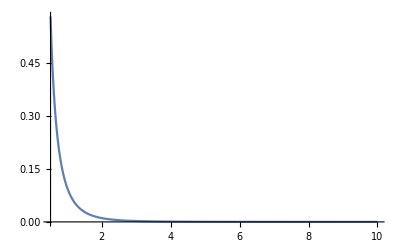

```mathematica
Plot[Out[42],{σ,pm,10},PlotRange->All]
```

```mathematica
approx = FunctionInterpolation[Out[110],{σ,pm,10}]
```

FunctionInterpolation::ncvb: FunctionInterpolation failed to meet the prescribed accuracy and precision goals after 6 recursive bisections near σ = {0.516334}. Continuing to refine elsewhere.

FunctionInterpolation::ncvb: FunctionInterpolation failed to meet the prescribed accuracy and precision goals after 6 recursive bisections near σ = {0.590426}. Continuing to refine elsewhere.

FunctionInterpolation::ncvb: FunctionInterpolation failed to meet the prescribed accuracy and precision goals after 6 recursive bisections near σ = {0.664517}. Continuing to refine elsewhere.

General::stop: Further output of FunctionInterpolation::ncvb will be suppressed during this calculation.

InterpolatingFunction[…]

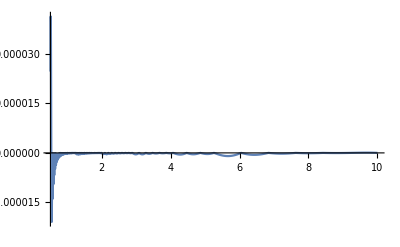

```mathematica
Plot[approx[σ]-(Out[110] ),{σ,0.516334,10.},PlotRange->All]
```

```mathematica
approx''[pm]
```

23.904

```mathematica
D[Out[73],σ]
```

-((2 p0 σ-(1+2 p0^2) (-p0/(√(1-((1+p0^2) (1-p0^2/σ^2))/(1+2 p0^2)) √(1-p0^2/σ^2) σ^2)+(2 p0 √(1-((1+p0^2) (1-p0^2/σ^2))/(1+2 p0^2)))/(√(1-p0^2/σ^2) σ^2)) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2))-(p0^2 σ^2 √(-p0^2+σ^2) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/(√((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)))-((1+2 p0^2) σ^2 √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/(√(-p0^2+σ^2))-(1+2 p0^2) √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/(√(1+p0^2) √(1/(1+2 p0^2)) σ^2 ((1+2 p0^2)/(1+σ^2))^(3/2) √((1+σ^2)^5-p0^2 (4+6 σ^2+4 σ^4+σ^6)-p0^4 (4+6 σ^2+4 σ^4+σ^6))))+((10 σ (1+σ^2)^4-p0^2 (12 σ+16 σ^3+6 σ^5)-p0^4 (12 σ+16 σ^3+6 σ^5)) (-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)])))/(2 √(1+p0^2) √(1/(1+2 p0^2)) σ^2 ((1+2 p0^2)/(1+σ^2))^(3/2) ((1+σ^2)^5-p0^2 (4+6 σ^2+4 σ^4+σ^6)-p0^4 (4+6 σ^2+4 σ^4+σ^6))^(3/2))+(2 (-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)])))/(√(1+p0^2) √(1/(1+2 p0^2)) σ^3 ((1+2 p0^2)/(1+σ^2))^(3/2) √((1+σ^2)^5-p0^2 (4+6 σ^2+4 σ^4+σ^6)-p0^4 (4+6 σ^2+4 σ^4+σ^6)))-(3 (-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)])))/(√(1+p0^2) (1/(1+2 p0^2))^(3/2) σ ((1+2 p0^2)/(1+σ^2))^(5/2) (1+σ^2)^2 √((1+σ^2)^5-p0^2 (4+6 σ^2+4 σ^4+σ^6)-p0^4 (4+6 σ^2+4 σ^4+σ^6)))

```mathematica
-(-2 (p0^3+p0^5)+p0 σ^2-(1+2 p0^2) σ √(-p0^2+σ^2) √((p0^2 (1+p0^2+σ^2))/(1+2 p0^2)) (2 EllipticE[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]-EllipticF[ArcCos[p0/σ],(1+p0^2)/(1+2 p0^2)]))/((1+2 p0^2) σ ^2 √(1+p0^2)  p0) /.p0->pm
```

-(1.1224 (-0.348709+0.516334 σ^2-0.639339 σ √(-0.266601+σ^2) √(1.2666+σ^2) (2 EllipticE[ArcCos[0.516334/σ],0.826115]-EllipticF[ArcCos[0.516334/σ],0.826115])))/σ^2

```mathematica
Series[Out[38],{σ,pm,5},Assumptions->{σ>pm>0}] //FullSimplify
```

0.888546-2.24481 (σ-0.516334)+4.3957 (σ-0.516334)^2-8.23262 (σ-0.516334)^3+15.5775 (σ-0.516334)^4-29.8899 (σ-0.516334)^5+O[σ-0.516334]^6

```mathematica
m = 0.8885462475876046-2.2448088683260674 (σ-0.5163344740613613)+4.395703682430362 (σ-0.5163344740613613)^2-8.232617306894241 (σ-0.5163344740613613)^3+15.577502704202487 (σ-0.5163344740613613)^4-29.889892648628944 (σ-0.5163344740613613)^5;
mm = D[m,σ];
mmm = D[mm,σ];
```

```mathematica
-2.2448088683260674 /0.8885462475876046
```

-2.52638

```mathematica
c1p/.{λ->0, P0->pm}
```

c[1]→-2.52638

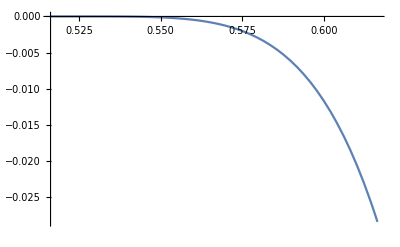

```mathematica
Plot[(2*(P0^2+P0^4)m/σ^2+(σ+2 (σ)^3)mm +(-P0^2-P0^4+(σ)^2+(σ)^4) mmm - 2 σ^2 m) /.P0->pm,{σ,pm,pm+0.1},PlotRange->All]
```

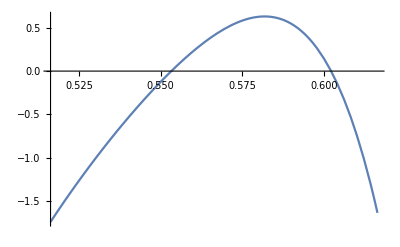

```mathematica
Plot[((2*(P0^2+P0^4)m/σ^2+(σ+2 (σ)^3)mm +(-P0^2-P0^4+(σ)^2+(σ)^4) mmm) /m)/.P0->pm,{σ,pm,pm+0.1},PlotRange->All]
```

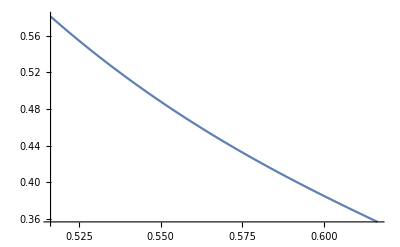

```mathematica
Plot[m,{σ,pm,pm+0.1}]
```

```mathematica
bc1
```

1.

```mathematica
bc2 /.{P0->pm,λ->0}
```

-3.19992

```mathematica
Out[42]/D[Out[42],σ] /.σ->pm
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Indeterminate

```mathematica
r = -1/2 + Sqrt[1/4-λ]
σ^r
```

```mathematica
DSolve[-scalarLaplacian[a[σ]] - (2 (P0^2+P0^4)/σ^4)*a[σ] ==0,a,σ]
```

$Aborted

```mathematica
N[Sinh[1/10]]
```

0.100167

```mathematica
Clear[zeroEigen]
```

```mathematica
zeroEigen[P0_] :=NDSolveValue[{a[1.01 P0]==1+(0.010000000000000009 (-2-2 P0^2))/(1+2 P0^2)+(0.000016666666666666695 (10+34 P0^2+24 P0^4))/((1+2 P0^2)^2), a'[1.01 P0]==(-2-2 P0^2)/(P0 (1+2 P0^2))+(0.003333333333333336 (10+34 P0^2+24 P0^4))/(P0 (1+2 P0^2)^2), 2*(P0^2+P0^4)a[σ]+(σ)^2(σ+2 (σ)^3)a'[σ] +(σ)^2(-P0^2-P0^4+(σ)^2+(σ)^4) a''[σ]==0},a[150000],{σ,1.01 P0,150000}]
```

```mathematica
zeroEigen[0.5163344740613613]
```

-1.01155

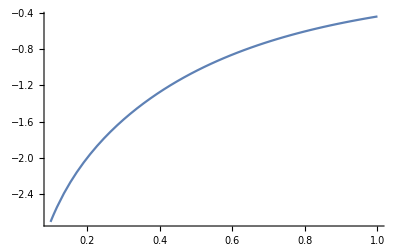

```mathematica
Plot[zeroEigen[p],{p,0.1,1}]
```

```mathematica
N[Sinh[5]]
```

74.2032

```mathematica
Integrate[4(1-w^2)/((1+w^2)(z^2-w^2)), {w,0,r},Assumptions->{r<z,0<r<1}]
```

(8 z ArcTan[r]+2 (-1+z^2) Log[1-(2 r)/(r+z)])/(z+z^3)

```mathematica
Integrate[w^2/(w-z),w]
```

1/2 (w-z)^2+2 (w-z) z+z^2 Log[w-z]

```mathematica
Integrate[w/((w^2+1)(z^2-w^2)),{w,0,r},Assumptions->{r<z,0<r<1}]
```

(-ArcTanh[1-(2 (1+r^2))/(1+z^2)]+Log[z])/(1+z^2)

```mathematica
Integrate[(1+w^2)/((w^2-z1^2)(w^2-z2^2)),{w,0,r},Assumptions->{0<r<1,r<z1<z2}]
```

(-((1+z1^2) z2 ArcTanh[r/z1])+z1 (1+z2^2) ArcTanh[r/z2])/(z1 z2 (z1^2-z2^2))

```mathematica
Integrate[(1-w^2)/((w^2-z1^2)(w^2-z2^2)),{w,0,r},Assumptions->{0<r<1,r<z1<z2}]
```

((z2-z1^2 z2) Log[1-(2 r)/(r+z1)]+z1 (-1+z2^2) Log[1-(2 r)/(r+z2)])/(2 z1 (z1-z2) z2 (z1+z2))

```mathematica
Integrate[w/((w^2-z1^2)(w^2-z2^2)),{w,0,r},Assumptions->{0<r<1,r<z1<z2}]
```

(-2 Log[z1]+2 Log[z2]+Log[(r^2-z1^2)/(r^2-z2^2)])/(2 (z1^2-z2^2))